```mathematica
ClearAll["Global`*"]
$Assumptions=β∈Reals&&Ω∈Reals&&Ω0∈Reals&&t∈Reals&&β>0 && Ω>0 &&t>0&&β<π/4&&ωL∈Reals&& ωL>0&&A∈Reals&&A>0&&B∈Reals&&B>0&& m∈PositiveIntegers&&k∈PositiveIntegers
```

β∈ℝ&&Ω∈ℝ&&Ω0∈ℝ&&t∈ℝ&&β>0&&Ω>0&&t>0&&β<π/4&&ωL∈ℝ&&ωL>0&&A∈ℝ&&A>0&&B∈ℝ&&B>0&&m∈ℤ&&m>0&&k∈ℤ&&k>0

```mathematica
(*build time evolution operator including off-resonant driving and perpendicular component*)
(*define Hamiltonian for both electron subspaces in RF with RWA, now driving resonantly as we would like to evaluate the error arising from the Aperp.*)
H0=((ωL*Cos[β]-ω)*Cos[β])/2*PauliMatrix[3]+(-ω*Sin[β]+Ω0*(Cos[β])^2*Cos[ϕ0+(m-1)*A*τ])/2*PauliMatrix[1]+(Ω0*Cos[β]*Sin[ϕ0+(m-1)*A*τ])/2*PauliMatrix[2]/.{ω->ωL-A,Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B^2/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
H1=((ω1-ω)*Cos[β]+Ω*Cos[β]*Sin[β]*Cos[ϕ1+(n-1)*A*τ])/2*PauliMatrix[3]+((ω1-ω)*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ1+(n-1)*A*τ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ1+(n-1)*A*τ])/2*PauliMatrix[2]/.{ω->ωL-A,Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B^2/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
H0 //MatrixForm
H1 //MatrixForm
```

(((-A+ωL) (A-ωL+(ωL (-A+ωL))/(√(B^2+(-A+ωL)^2))))/(2 √(B^2+(-A+ωL)^2)) | 1/2 (-(B^2 (-A+ωL))/(√(B^2+(-A+ωL)^2))+(Ω0 (-A+ωL)^2 Cos[A (-1+m) τ+ϕ0])/(B^2+(-A+ωL)^2))-(ⅈ Ω0 (-A+ωL) Sin[A (-1+m) τ+ϕ0])/(2 √(B^2+(-A+ωL)^2))
1/2 (-(B^2 (-A+ωL))/(√(B^2+(-A+ωL)^2))+(Ω0 (-A+ωL)^2 Cos[A (-1+m) τ+ϕ0])/(B^2+(-A+ωL)^2))+(ⅈ Ω0 (-A+ωL) Sin[A (-1+m) τ+ϕ0])/(2 √(B^2+(-A+ωL)^2)) | -((-A+ωL) (A-ωL+(ωL (-A+ωL))/(√(B^2+(-A+ωL)^2))))/(2 √(B^2+(-A+ωL)^2)))

(1/2 (((-A+ωL) (A-ωL+√(B^2+(-A+ωL)^2)))/(√(B^2+(-A+ωL)^2))+(B^2 Ω (-A+ωL) Cos[A (-1+n) τ+ϕ1])/(B^2+(-A+ωL)^2)) | 1/2 ((B^2 (A-ωL+√(B^2+(-A+ωL)^2)))/(√(B^2+(-A+ωL)^2))+(Ω (-A+ωL)^2 Cos[A (-1+n) τ+ϕ1])/(B^2+(-A+ωL)^2))-(ⅈ Ω (-A+ωL) Sin[A (-1+n) τ+ϕ1])/(2 √(B^2+(-A+ωL)^2))
1/2 ((B^2 (A-ωL+√(B^2+(-A+ωL)^2)))/(√(B^2+(-A+ωL)^2))+(Ω (-A+ωL)^2 Cos[A (-1+n) τ+ϕ1])/(B^2+(-A+ωL)^2))+(ⅈ Ω (-A+ωL) Sin[A (-1+n) τ+ϕ1])/(2 √(B^2+(-A+ωL)^2)) | 1/2 (-((-A+ωL) (A-ωL+√(B^2+(-A+ωL)^2)))/(√(B^2+(-A+ωL)^2))-(B^2 Ω (-A+ωL) Cos[A (-1+n) τ+ϕ1])/(B^2+(-A+ωL)^2)))

```mathematica
(*test: do we get correct dynamics with B=0?*)
H0check=((ωL*Cos[β]-ω)*Cos[β])/2*PauliMatrix[3]+(-ω*Sin[β]+Ω0*(Cos[β])^2*Cos[ϕ0+(m-1)*A*τ])/2*PauliMatrix[1]+(Ω0*Cos[β]*Sin[ϕ0+(m-1)*A*τ])/2*PauliMatrix[2]/.{ω->ωL-A,Cos[β]->1,Sin[β]->0, ω1->ωL-A};
H1check=((ω1-ω)*Cos[β]+Ω*Cos[β]*Sin[β]*Cos[ϕ1+(n-1)*A*τ])/2*PauliMatrix[3]+((ω1-ω)*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ1+(n-1)*A*τ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ1+(n-1)*A*τ])/2*PauliMatrix[2]/.{ω->ωL-A,Cos[β]->1,Sin[β]->0, ω1->ωL-A};
H0check //MatrixForm
H1check //MatrixForm
(*passt!*)
```

(A/2 | 1/2 Ω0 Cos[A (-1+m) τ+ϕ0]-1/2 ⅈ Ω0 Sin[A (-1+m) τ+ϕ0]
1/2 Ω0 Cos[A (-1+m) τ+ϕ0]+1/2 ⅈ Ω0 Sin[A (-1+m) τ+ϕ0] | -A/2)

(0 | 1/2 Ω Cos[A (-1+n) τ+ϕ1]-1/2 ⅈ Ω Sin[A (-1+n) τ+ϕ1]
1/2 Ω Cos[A (-1+n) τ+ϕ1]+1/2 ⅈ Ω Sin[A (-1+n) τ+ϕ1] | 0)

```mathematica
(*Now define time evolution operator as function and build entire sequence of alternating operators*)
U0f[t_,m_,ϕ0_]:=MatrixExp[-ⅈ*({{((-A+ωL) (A-ωL+(ωL (-A+ωL))/(√(B^2+(-A+ωL)^2))))/(2 √(B^2+(-A+ωL)^2)), 1/2 (-(B^2 (-A+ωL))/(√(B^2+(-A+ωL)^2))+(Ω0 (-A+ωL)^2 Cos[A (-1+m) τ+ϕ0])/(B^2+(-A+ωL)^2))-(ⅈ Ω0 (-A+ωL) Sin[A (-1+m) τ+ϕ0])/(2 √(B^2+(-A+ωL)^2))}, {1/2 (-(B^2 (-A+ωL))/(√(B^2+(-A+ωL)^2))+(Ω0 (-A+ωL)^2 Cos[A (-1+m) τ+ϕ0])/(B^2+(-A+ωL)^2))+(ⅈ Ω0 (-A+ωL) Sin[A (-1+m) τ+ϕ0])/(2 √(B^2+(-A+ωL)^2)), -((-A+ωL) (A-ωL+(ωL (-A+ωL))/(√(B^2+(-A+ωL)^2))))/(2 √(B^2+(-A+ωL)^2))}})*t];
U1f[t_,n_,ϕ1_] :=MatrixExp[-ⅈ*({{1/2 (((-A+ωL) (A-ωL+√(B^2+(-A+ωL)^2)))/(√(B^2+(-A+ωL)^2))+(B^2 Ω (-A+ωL) Cos[A (-1+n) τ+ϕ1])/(B^2+(-A+ωL)^2)), 1/2 ((B^2 (A-ωL+√(B^2+(-A+ωL)^2)))/(√(B^2+(-A+ωL)^2))+(Ω (-A+ωL)^2 Cos[A (-1+n) τ+ϕ1])/(B^2+(-A+ωL)^2))-(ⅈ Ω (-A+ωL) Sin[A (-1+n) τ+ϕ1])/(2 √(B^2+(-A+ωL)^2))}, {1/2 ((B^2 (A-ωL+√(B^2+(-A+ωL)^2)))/(√(B^2+(-A+ωL)^2))+(Ω (-A+ωL)^2 Cos[A (-1+n) τ+ϕ1])/(B^2+(-A+ωL)^2))+(ⅈ Ω (-A+ωL) Sin[A (-1+n) τ+ϕ1])/(2 √(B^2+(-A+ωL)^2)), 1/2 (-((-A+ωL) (A-ωL+√(B^2+(-A+ωL)^2)))/(√(B^2+(-A+ωL)^2))-(B^2 Ω (-A+ωL) Cos[A (-1+n) τ+ϕ1])/(B^2+(-A+ωL)^2))}})*t];
```

```mathematica
Transpose[Conjugate[U0]].U0
Transpose[Conjugate[U1]].U1
```

Transpose[Conjugate[U0]].U0

Transpose[Conjugate[U1]].U1

```mathematica
U2V0[t_,n_,ϕ1_, m_,ϕ0_]:=U1f[t,n,ϕ1].U0f[t,m,ϕ0];
U2V1[t_,m_,ϕ0_, n_,ϕ1_]:=U0f[t,m,ϕ0].U1f[t,n,ϕ1];
```

```mathematica
(*#################################################################################*)
(*#################################################################################*)
```

```mathematica
(*first test: in case of no off-resonant driving and no perpendicular component, do we get a CNOT? -> we do. It was the entire calculation below with B=0.*)
(*so now, it is possible to look at the fidelty for different values of B*)
M=4;
Ω0=Ω;
```

```mathematica
(*in this version, the free evolution with the phase Aτ is taken into account and corrected*)
V0table=Table[U2V0[2*τ,i,0,i-1,π],{i,M,4,-2}]/.{τ->π/(2*M*Ω)};
PrependTo[V0table,U0f[τ,M+1, π]/.{τ->π/(2*M*Ω)}];
AppendTo[V0table,U1f[2*τ,2,0]/.{τ->π/(2*M*Ω)}];
AppendTo[V0table,U0f[τ,1,π]/.{τ->π/(2*M*Ω)}];
V0table;
V0=Dot @@ V0table ;
V1table=Table[U2V1[2*τ,i,0,i-1,π],{i,M,4,-2}]/.{τ->π/(2*M*Ω)};
PrependTo[V1table,U1f[τ,M+1, π]/.{τ->π/(2*M*Ω)}];
AppendTo[V1table,U0f[2*τ,2,0]/.{τ->π/(2*M*Ω)}];
AppendTo[V1table,U1f[τ,1,π]/.{τ->π/(2*M*Ω)}];
V1table;
V1=Dot @@ V1table ;
```

```mathematica
VOR=KroneckerProduct[{{1,0},{0,0}},V0]+KroneckerProduct[{{0,0},{0,1}},V1];
VZ=KroneckerProduct[IdentityMatrix[2],MatrixExp[-PauliMatrix[3]*ⅈ*(N*A*τg)/2]]/.τg->π/(2*N*Ω);
VZ†=FullSimplify[ConjugateTranspose[VZ], Assumptions->{A ∈ Reals,Ω∈ Reals}];
```

```mathematica
VcnotOR=Exp[-ⅈ*π/4]*KroneckerProduct[IdentityMatrix[2],MatrixExp[PauliMatrix[1]*ⅈ*π/4]].KroneckerProduct[MatrixExp[PauliMatrix[3]*ⅈ*π/4],IdentityMatrix[2]].VZ†.VOR;
Ucnot={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}};
```

```mathematica
Fav=(Abs[Tr[Ucnot.VcnotOR]]^2+4)/20/.{τ->π/(2*M*Ω),A->200,B->2,ωL->430};
```

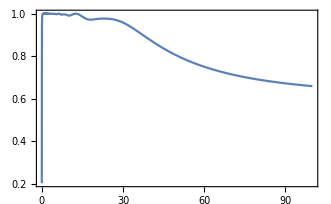

```mathematica
Plot[{Fav},{Ω,0,100},Frame->True]
```

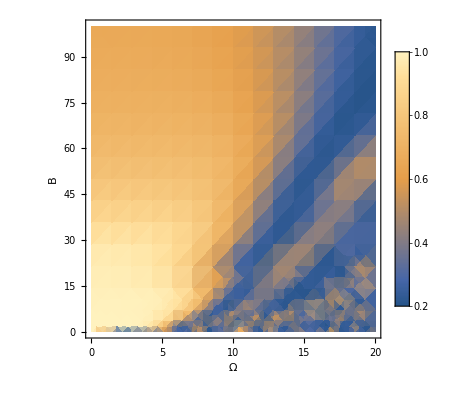

```mathematica
Fav2dplot=(Abs[Tr[Ucnot.VcnotOR]]^2+4)/20/.{τ->π/(2*M*Ω),A->190,ωL->430};
DensityPlot[Fav2dplot,{B,0,20},{Ω,0,100},PlotLegends->Automatic,AxesLabel->{Ω,B}]
```